```mathematica
(Subscript[s, 1]-h Tan[ϕ]-x)^2+(Subscript[s, 2]+h Tan[ϕ]-x)^2
```

(-x+s_1-h Tan[ϕ])^2+(-x+s_2+h Tan[ϕ])^2

```mathematica
%//Simplify
```

s_1^2+s_2^2-2 s_2 (x-h Tan[ϕ])-2 s_1 (x+h Tan[ϕ])+2 (x^2+h^2 Tan[ϕ]^2)

```mathematica
%//Expand
```

2 x^2-2 x s_1+s_1^2-2 x s_2+s_2^2-2 h s_1 Tan[ϕ]+2 h s_2 Tan[ϕ]+2 h^2 Tan[ϕ]^2

```mathematica
Exp[%]
```

ⅇ^(s_1^2+s_2^2-2 s_2 (x-h Tan[ϕ])-2 s_1 (x+h Tan[ϕ])+2 (x^2+h^2 Tan[ϕ]^2))

```mathematica
Integrate[%,{ϕ,-Pi/2,Pi/2}]
```

$Aborted

```mathematica
Integrate[Exp[(A-Tan[ϕ])^2],{ϕ,-Pi/2,Pi/2}]
```

Integrate::idiv: Integral of ⅇ^(A - Tan[ϕ])^2 does not converge on {-π/2, π/2}.

∫_(-π/2)^(π/2) ⅇ^((A-Tan[ϕ])^2)ⅆϕ

```mathematica
2 h Subscript[s, 1] Tan[ϕ]+2 h Subscript[s, 2] Tan[ϕ]+2 h^2 Tan[ϕ]^2
```

2 h s_1 Tan[ϕ]+2 h s_2 Tan[ϕ]+2 h^2 Tan[ϕ]^2

```mathematica
(A+B Tan[ϕ])^2 //Expand
```

A^2+2 A B Tan[ϕ]+B^2 Tan[ϕ]^2

```mathematica
Series[-(A-Tan[ϕ])^2/(2σ^2),{ϕ,ArcTan[A],4}]
```

((-1-2 A^2-A^4) (ϕ-ArcTan[A])^2)/(2 σ^2)+((-A-2 A^3-A^5) (ϕ-ArcTan[A])^3)/σ^2+((-2-13 A^2-20 A^4-9 A^6) (ϕ-ArcTan[A])^4)/(6 σ^2)+O[ϕ-ArcTan[A]]^5

```mathematica
Integrate[Exp[((-1-2 A^2-A^4) (ϕ-ArcTan[A])^2)/(2 σ^2)],{ϕ,-Infinity,Infinity}
```

```mathematica
1/(h Tan'[ArcTan[s/h]]) //Simplify
```

h/(h^2+s^2)

```mathematica
n=100000
```

100000

```mathematica
dat=Tan[RandomReal[{-Pi/2,Pi/2},{n}]];
```

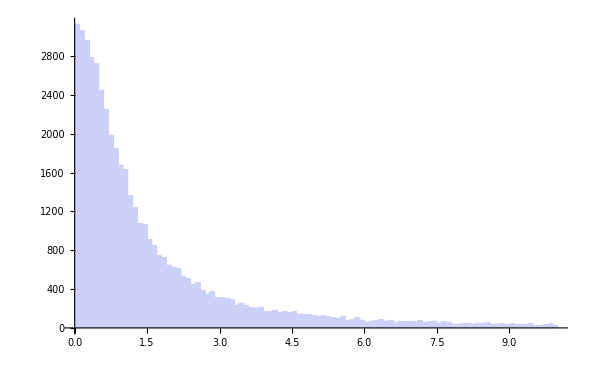

```mathematica
hist=Histogram[dat,{0,10,0.1}]
```

```mathematica
Integrate[1/π h/(h^2+s^2),{s,0,Infinity},Assumptions->h>0]
```

1/2

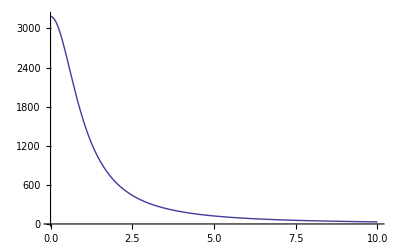

```mathematica
prob=Plot[0.1 n 1/π 1/(1+s^2),{s,0,10},PlotRange->All]
```

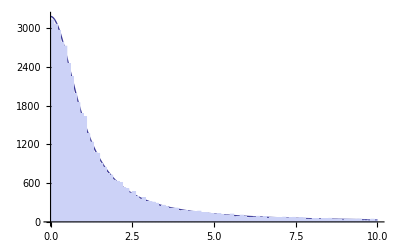

```mathematica
Show[prob,hist]
```

```mathematica
Integrate[Exp[-(Subscript[s, 1]-s-x)^2 -(Subscript[s, 2]+s-x)^2 ]/(1+s^2),{s,-Infinity,Infinity}]
```

∫_(-∞)^∞ (ⅇ^(-(-s-x+s_1)^2-(s-x+s_2)^2))/(1+s^2)ⅆs

```mathematica
-(Subscript[s, 1]-s-x)^2 -(Subscript[s, 2]+s-x)^2 //Expand
```

-2 s^2-2 x^2+2 s s_1+2 x s_1-s_1^2-2 s s_2+2 x s_2-s_2^2

```mathematica
Integrate[Exp[-(s-A)^2]/(1+s^2),{s,-Infinity,Infinity}]
```

∫_(-∞)^∞ (ⅇ^(-(-A+s)^2))/(1+s^2)ⅆs

```mathematica
D[-2 x A -2 m x^2 -B ,x]
```

-2 A-4 m x

```mathematica
P={0,1}
Subscript[P, l]={-a,1}-{x,0}
Subscript[P, r]={a,1}-{x,0}
```

{0,1}

{-a-x,1}

{a-x,1}

```mathematica
P.Subscript[P, l]/(Norm[P].Norm[Subscript[P, l]])
```

1/(1.√(1+Abs[-a-x]^2))

```mathematica
1/Sqrt[1+(a+x)^2]-1/Sqrt[1+(a-x)^2]
```

-1/(√(1+(a-x)^2))+1/(√(1+(a+x)^2))

```mathematica
%95+O[x]^4
```

-(2 a x)/((1+a^2)^(3/2))+((3 a-2 a^3) x^3)/((1+a^2)^(7/2))+O[x]^4

```mathematica
α=ArcTan[x]
β=ArcCot[1-x]
```

ArcTan[x]

ArcCot[1-x]

```mathematica
Subscript[q, 1]=π/2-α-β
Subscript[q, 2]=2 α
Subscript[q, 3]=Subscript[q, 1]
```

π/2-ArcCot[1-x]-ArcTan[x]

2 ArcTan[x]

π/2-ArcCot[1-x]-ArcTan[x]

```mathematica
Z=Subscript[q, 1]+Subscript[q, 2]+Subscript[q, 3]
```

π-2 ArcCot[1-x]

```mathematica
Subscript[p, 1]=Subscript[q, 1]/Z
Subscript[p, 2]=Subscript[q, 2]/Z
Subscript[p, 3]=Subscript[q, 3]/Z
```

(π/2-ArcCot[1-x]-ArcTan[x])/(π-2 ArcCot[1-x])

(2 ArcTan[x])/(π-2 ArcCot[1-x])

(π/2-ArcCot[1-x]-ArcTan[x])/(π-2 ArcCot[1-x])

```mathematica
D[Sum[Subscript[m, i] Log[Subscript[p, i]],{i,1,3}],x]//FullSimplify
```

(((2+(-2+x) x) (π-2 ArcCot[1-x])+2 (1+x^2) ArcTan[x]) ((π-2 ArcCot[1-x]) m_2-2 ArcTan[x] (m_1+m_2+m_3)))/((2+(-2+x) x) (1+x^2) (π-2 ArcCot[1-x]) (π-2 ArcCot[1-x]-2 ArcTan[x]) ArcTan[x])

```mathematica
((2+(-2+x) x) (π-2 ArcCot[1-x])+2 (1+x^2) ArcTan[x]) ((π-2 ArcCot[1-x]) Subscript[m, 2]-2 ArcTan[x] (Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]))
```

((2+(-2+x) x) (π-2 ArcCot[1-x])+2 (1+x^2) ArcTan[x]) ((π-2 ArcCot[1-x]) m_2-2 ArcTan[x] (m_1+m_2+m_3))

```mathematica
Solve[(π-2 ArcCot[1-x]) Subscript[m, 2]-2 ArcTan[x] (Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3])==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(π-2 ArcCot[1-x]) m_2-2 ArcTan[x] (m_1+m_2+m_3)==0,x]

```mathematica
Tan[Pi/2-x]
```

Cot[x]

```mathematica
ArcTan[x] -(Pi/2-ArcCot[x]) //TrigReduce
```

-π/2+ArcCot[x]+ArcTan[x]

```mathematica
Solve[A ArcTan[1-x]==B ArcTan[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
ArcTan[1-x]A - ArcTan[x]
```

A ArcTan[1-x]-ArcTan[x]

```mathematica
%+O[x]^3
```

(A π)/4+(-1-A/2) x-(A x^2)/4+O[x]^3

```mathematica
%//Normal
```

(A π)/4+(-1-A/2) x-(A x^2)/4

```mathematica
Solve[%==0,x]
```

{{x→(-4-2 A-√((-4-2 A)^2+4 A^2 π))/(2 A)},{x→(-4-2 A+√((-4-2 A)^2+4 A^2 π))/(2 A)}}

```mathematica
%//Simplify
```

{{x→-(2+A+√(4+4 A+A^2 (1+π)))/A},{x→(-2-A+√(4+4 A+A^2 (1+π)))/A}}

```mathematica
ArcTan[x]/ArcTan[1-x]
```

ArcTan[x]/ArcTan[1-x]

```mathematica
%146+O[x]^2
```

(4 x)/π+O[x]^2

```mathematica
hit[ϕ_,x_]:=Module[{s=Tan[ϕ],up,dn},up=x-s;dn=x+s;
Which[
up<0 && up>-1 && dn<1,1,
up>0 && up <1 && dn >0 && dn < 1, 2,
up>0 && up <1 && dn <0 && dn > -1, 3,
True,0]

]
```

```mathematica
stat=hit[#,.1]&/@RandomReal[{-Pi/2,Pi/2},{1000}];
```

```mathematica
bin=BinCounts[stat,{0,4,1}]
```

{530,206,72,192}

```mathematica
a=bin[[3]]/Total[Take[bin,{2,4}]]//N
```

0.153191

```mathematica
FindRoot[a==ArcTan[x]/ArcTan[1-x],{x,.1}]
```

{x→0.111724}